# Project report

## Retained material: Cold spots?

D Malan

Department of Chemistry
University of Pretoria

26 January 2020

## Introduction

I would like to work further with the Total™ 50 ppm diesel, both to spike with PAHs and to blend with biodiesel. But on injecting replicates I found a rather nasty feature in the chromatography, which I need to get rid of until before I can continue.

I did a single run with the Shell™ 50 ppm diesel, to get an idea of what the aromatics portion should look like. This was made a very pretty chromatogram. When I blended the RME biodiesel, I got strange results in the alkanes. There was wraparound, which spoiled the chromatogram. First I thought it might be waxes from the biodiesel, that just eluted too late. But extending the GC run time (in particular, the hold at the 350 °C top) showed a huge alkane peak. This can’t be material from the biodiesel, which is only present at 7%. In any case, when I then injected pure diesel (taken directly from the sample container to exclude the possibility of contamination during storage in a vial) the hump was still there.

There were no major changes to the chromatograph between the successful run and the problematic ones, so careful thinking lead me to suspect that some of the analyte might be trapped in the inlet manifold.

## Experimental

I injected Total™ 50 ppm diesel, collecting 2 s fractions. For the “pretty” run I used a 20 °C to 350 °C ramp, with a 2 s hold. For the “ugly” run I used a 20 °C to 350 °C ramp, with a 12 s hold.

## Results

Here' s the pretty Total™ 50 ppm diesel picture:

-Graphics3D-

And here’s the “ugly” one with the hump:

-Graphics3D-

My current suspicion is that material gets trapped on a cold spot the inlet-end manifold. To examine the possibility I got the manifold temperature data:

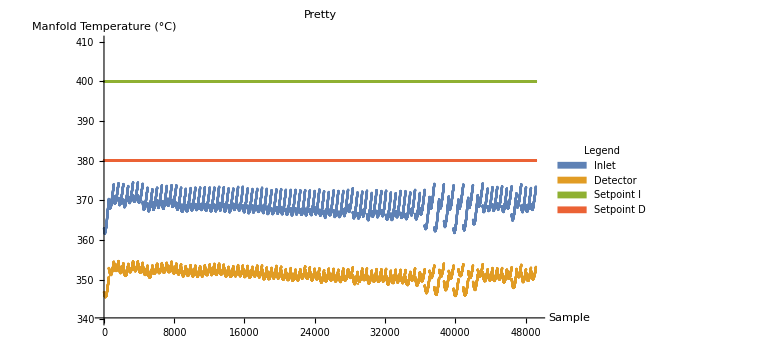

```mathematica
"2020_01_22-174010.dat"
```

```mathematica
"2020_01_25-173343.dat"
```

-Graphics-

## Discussion

The data does not contradict the idea of a cold spot trapping material. In the “pretty” chromatogram the peaks on the alkane hump goes to the end of the hump. In the “ugly” one they are obliterated just after the peak of the hump. At this time the manifold is heating up nicely, and the program temperature is high enough for material to elute. But because it’s not focused on a little spot, it’s spread out. Because the heaviest material is trapped best, it elutes in a hump or two, isothermically.

The temperature records of the manifolds does not contradict the idea of a cold spot. Interpreting this data requires some care: this is the temperature of a thermocouple in the block of the manifold. The actual temperature of the column is probably lower than the reported temperature. This is reinforced by the fact the the temperature measurement is still going down for a few seconds after the cooling has stopped. This means that the temperature of the core of the block is lower than the temperature of the thermocouple .  Although the average temperature in both cases are 370 °C, in the case of the “ugly” run the swing is much larger. The minimum temperature of the inlet-end manifold is higher for the “pretty” run. This indicates more cooling during the “ugly” run, which means the cold spot idea is not eliminated.

In both the temperature records the temperature swing in the detector-end manifold is smaller than in the inlet-end manifold. This means that the cooling is less, which might mean that no trapping takes place there, despite the lower average temperature. Again, in the “ugly” run the temperature swing is larger, which show that the manifold cooling is linked to total cryogen flow.  Of course, any trapping in the detector-end manifold will not contribute to wraparound, although it might interfere with a good peak shape.

I wonder if there’s a thing like a “trapping threshold temperature.”

If a cold spot in the inlet-end manifold is indeed the problem, then at least two options for mitigation  may be considered:

Increase the set temperature.

Adjust the cryogen flow.

Both are viable. In a previous report I’ve mentioned that high temperature set points do not seem to damage the column. Adjusting the cryogen flow is also possible, and it would be interesting to see if a higher flow or a lower flow will lead to less cooling in the inlet-end manifold. If the changed flow leads to a higher column trapping temperature (say up to 0 °C), I’m sure that won’t do any harm either.

## Conclusion

It is possible that the SFC×GC chromatograms are spoiled by material being trapped in a cold spot in the inlet manifold. This cold spot is perhaps caused by excessive cooling during cryogen flow periods.

## Recommendations

Redesign the manifold, so that coolant for the column does not cool the transfer line.

Use a more appropriate temperature control algorithm. Feedforward seems to be indicated: if the cooling starts we know that more heat will be needed. We don’t need to wait for the temperature of the manifold to drop before we add more power.

Isolate the coaxial heater thermally. If the column is held cold passively no coolant needs to flow during trapping.

Find the cryogen flow rate that minimizes manifold cooling. Column trapping temperature can be sacrificed for higher manifold temperatures.

Find a way to measure and record the cryogen flow rate.

Increase the inlet-end manifold temperature set point, so that it has a higher average temperature.